### data reading

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039, 0.03105 ,0.025, 0.016, 0.01 ,0.008, 0.0063 ,0.005, 0.00385 ,0.0031 ,0.0028},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015,0.001},{0.039, 0.016 ,0.01 ,0.005, 0.00385 ,0.0025, 0.002, 0.001, 0.0005, 0.00033, 0.00025 ,0.00014 ,0.000091, 0.000077,0.000054, 0.000045 ,0.000036}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 3, 4,8, 15, 40,70,150, 250, 600,2000 ,2500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{2 ,4,10, 20, 40,60, 80,200, 500 ,800 ,1400, 2500 ,4200 ,5000, 6000,8500, 9500}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
fitting={{FittedModel[0.23898763148144703 ⅇ^(-0.7211106123773332 t^0.9905357466803566)],FittedModel[0.22123964351289824 ⅇ^(-0.5081162986880765 t^0.9511396339070934)],FittedModel[0.1813696719780106 ⅇ^(-0.3507298388051473 t^0.9930494750768472)],FittedModel[0.16577791128195302 ⅇ^(-0.2912303418610043 t^0.9879292979090472)],FittedModel[0.14411751794695463 ⅇ^(-0.20788463714685138 t^0.9022831799281819)],FittedModel[0.09658280354484236 ⅇ^(-0.11581857257786517 t^0.8828882669751839)],FittedModel[0.08760721415971362 ⅇ^(-0.09637245640731837 t^0.8159026294982501)],FittedModel[0.07020110194421185 ⅇ^(-0.07511334107606668 t^0.8062337510106476)],FittedModel[0.05937561134616735 ⅇ^(-0.08317315106749175 t^0.6845737695316122)],FittedModel[0.048836380452269366 ⅇ^(-0.05075987031382538 t^0.6526187775027247)],FittedModel[0.03569699202636103 ⅇ^(-0.03166533694389245 t^0.6690148855945094)],FittedModel[0.03531848519915478 ⅇ^(-0.021074994886229558 t^0.6679971822938536)]},{FittedModel[0.210469118046167 ⅇ^(-0.7938673305375744 t^0.9970053134440804)],FittedModel[0.2002748961300614 ⅇ^(-0.5586240727804905 t^0.9813348589407216)],FittedModel[0.1806273537862311 ⅇ^(-0.4765595231428065 t^0.981078261470334)],FittedModel[0.10014608113788581 ⅇ^(-0.20232201307994113 t^0.9818746605677192)],FittedModel[0.07772934947715844 ⅇ^(-0.15394721380219303 t^0.9020537793550232)],FittedModel[0.06450524342378627 ⅇ^(-0.11782315045472638 t^0.9257557768211936)],FittedModel[0.05866414366896228 ⅇ^(-0.14134027263292148 t^0.8050483006655912)],FittedModel[0.047727724274976464 ⅇ^(-0.09356640760732075 t^0.8333036600243768)],FittedModel[0.03666066589187361 ⅇ^(-0.04938993543886252 t^0.915321448104085)],FittedModel[0.033797253182206444 ⅇ^(-0.0785185119281658 t^0.7432280394330144)],FittedModel[0.02949867341512681 ⅇ^(-0.11162507608036888 t^0.6279151641455616)],FittedModel[0.021193773072896997 ⅇ^(-0.03587731515162103 t^0.7888937213495182)],FittedModel[0.014743317364245908 ⅇ^(-0.03385560869970338 t^0.740276023641977)],FittedModel[0.011383487326596189 ⅇ^(-0.028682081067680207 t^0.639651869424772)]},{FittedModel[0.20799883964240143 ⅇ^(-0.8098184268914607 t^0.8354901079758212)],FittedModel[0.09401287222906148 ⅇ^(-0.29637945294085394 t^0.9275525318989086)],FittedModel[0.06313653974466157 ⅇ^(-0.18332252277836303 t^0.9439680250792427)],FittedModel[0.032683434191457084 ⅇ^(-0.08515922061763434 t^0.9711616582929677)],FittedModel[0.026236025213799096 ⅇ^(-0.07365365468953826 t^0.9148415158760231)],FittedModel[0.01917806521076566 ⅇ^(-0.06719555510866196 t^0.8488661795607308)],FittedModel[0.015066655548010347 ⅇ^(-0.03366425858030262 t^0.962263099308754)],FittedModel[0.009576548285157518 ⅇ^(-0.03450816470500544 t^0.796073568867949)],FittedModel[0.006344614093174089 ⅇ^(-0.0510752015177966 t^0.6280369262479917)],FittedModel[0.004242003291775964 ⅇ^(-0.03429485944928721 t^0.6423945269492174)],FittedModel[0.003308193342826314 ⅇ^(-0.031095739318193923 t^0.5823399541578139)],FittedModel[0.002484664423852477 ⅇ^(-0.0227353904306616 t^0.5710769222392241)],FittedModel[0.0019862087870626296 ⅇ^(-0.058420745418723295 t^0.4762657335117356)],FittedModel[0.0015874086983166163 ⅇ^(-0.04941404523698897 t^0.46712210614533833)],FittedModel[0.001506007590506098 ⅇ^(-0.042821039473438904 t^0.4917684765642241)],FittedModel[0.0015355849211028693 ⅇ^(-0.031965478941523136 t^0.47127628259879484)],FittedModel[0.0013497999360571802 ⅇ^(-0.049712807316666954 t^0.47276345232658007)]}};
```

```mathematica
tauAlphaCRSISF={{1.4828695175315119,3.8256933758953924,4.893037452029123,6.385225894660054,14.242048873569146,46.53436035147325,66.08736938361386,123.70628209646453,224.16235801811828,540.5718664661808,1792.4734876850134,2629.3095653153127,4961.04642649804,7943.286898989977},{2.110569810297886,2.8535635003878395,4.877343904624338,9.579406366561173,20.31681995228492,31.37887939685443,43.85628627784445,58.31882259216383,88.39646313704145,128.2374800415089,181.51965991720982,263.17149572843937,475.00841743587415,1196.5949410110738,4927.942637083626,11646.981201916327},{3.1017846350890483,5.5358132780163976,6.040504798105056,14.37154943375042,26.619134777309572,46.625808864363535,75.98761972157511,198.80044236060098,534.2671053046677,1296.599916227994,2170.7599062350096,3986.378791798566,9994.46044163548,15655.445136823872,24221.649287166798,31978.611076271245,40190.13303119754}}
```

{{1.48287,3.82569,4.89304,6.38523,14.242,46.5344,66.0874,123.706,224.162,540.572,1792.47,2629.31,4961.05,7943.29},{2.11057,2.85356,4.87734,9.57941,20.3168,31.3789,43.8563,58.3188,88.3965,128.237,181.52,263.171,475.008,1196.59,4927.94,11647.},{3.10178,5.53581,6.0405,14.3715,26.6191,46.6258,75.9876,198.8,534.267,1296.6,2170.76,3986.38,9994.46,15655.4,24221.6,31978.6,40190.1}}

```mathematica
tauCRoverlap={{5.833319418117253,11.86278894161065,16.917338892978847,23.25548620200179,52.160702899712064,144.03673884723923,226.53383746332744,388.1550799983505,724.5750497347012,1566.498812260033,3781.0544591126413,5197.718904387892,9467.910598016313,16829.017670811918},{4.908732268246582,9.31848873794692,13.186591725727347,32.26259187830922,66.35481014996512,100.38226732553892,143.960577154809,209.23274864109732,333.8968037849868,460.04501744315485,668.6308529783303,958.8992763643564,1725.6436531887025,4336.275018528646,13857.138919303605,33009.675825311846},{7.834976775992932,22.460497359787702,40.922793734483406,94.78280185436874,128.79453931137476,231.55461796962314,323.17926259327726,843.8681996277791,2586.1167985909237,5036.916402039757,7314.717671434624,18600.880936529808,40307.93498223004,52624.590535830495,98462.79050610549,139254.67185534368,202268.02162912188}};
```

```mathematica
tauG={{1.3910888182410783,2.0377065818810434,2.8721829446497757,3.4858559446186668,5.702392407857531,11.492327980866376,17.591558728689055,24.80204778079744,37.81364943060074,96.27544933274132,174.27274958716865,323.1027895610921},{1.2605300263303496,1.8100483532785565,2.1285845112146036,5.090579906546081,7.959108649428122,10.075237157778854,11.3633647859236,17.167221813468228,26.74337026835027,30.67575625252056,32.84791292575899,67.9058468977229,96.88237145464551,257.8071625241086},{1.2872147966801697,3.7102550881880547,6.032789170571961,12.633822113258873,17.308263118561097,24.068114672781892,33.930534029921866,68.6454623635143,113.99068435628666,190.62220699117262,387.5690862311094,754.2955921779784,388.8658538190052,625.4075064615829,606.0297116868732,1489.063773376252,571.8207412602179}}
```

{{1.39109,2.03771,2.87218,3.48586,5.70239,11.4923,17.5916,24.802,37.8136,96.2754,174.273,323.103},{1.26053,1.81005,2.12858,5.09058,7.95911,10.0752,11.3634,17.1672,26.7434,30.6758,32.8479,67.9058,96.8824,257.807},{1.28721,3.71026,6.03279,12.6338,17.3083,24.0681,33.9305,68.6455,113.991,190.622,387.569,754.296,388.866,625.408,606.03,1489.06,571.821}}

```mathematica
Flatten[tauAlphaCRSISF]
```

{5.83332,11.8628,16.9173,23.2555,52.1607,144.037,226.534,388.155,724.575,1566.5,3781.05,5197.72,9467.91,16829.,4.90873,9.31849,13.1866,32.2626,66.3548,100.382,143.961,209.233,333.897,460.045,668.631,958.899,1725.64,4336.28,13857.1,33009.7,7.83498,22.4605,40.9228,94.7828,128.795,231.555,323.179,843.868,2586.12,5036.92,7314.72,18600.9,40307.9,52624.6,98462.8,139255.,202268.}

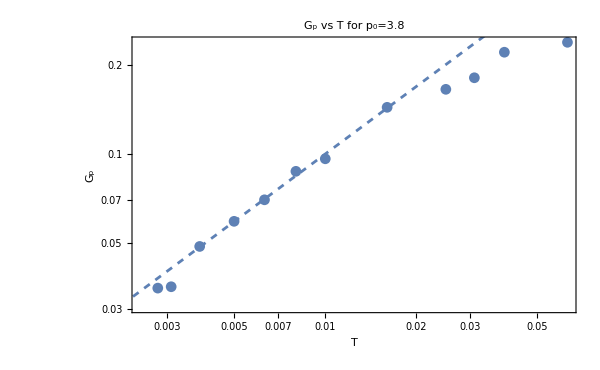
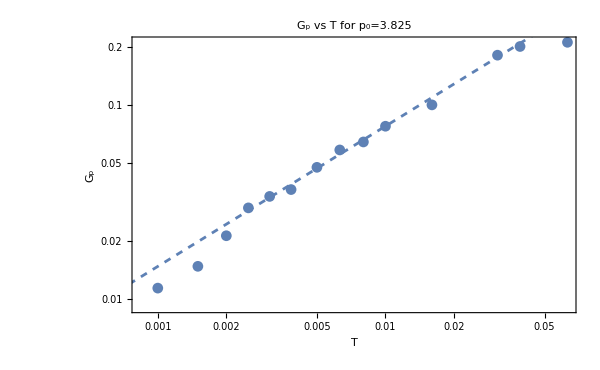
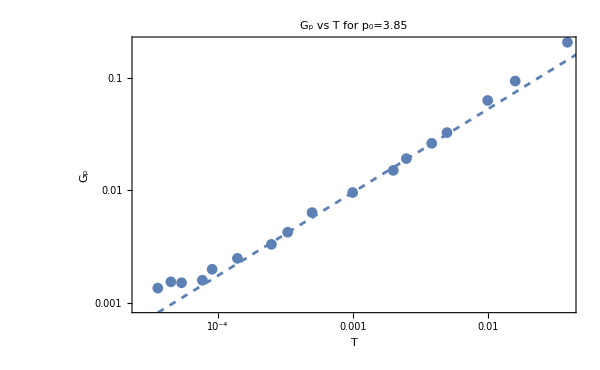

```mathematica
GPlots=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],fitting[[p,T]]["BestFitParameters"][[1,2]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"T","G_p"},ImageSize->600,PlotLabel->"G_p vs T for p_0="<>ToString[p0s[[p]]]],LogLogPlot[Gpfits[[p,2]][x],{x,10^-6,0.7},PlotStyle->Dashed]],{p,Length[p0s]}]
```

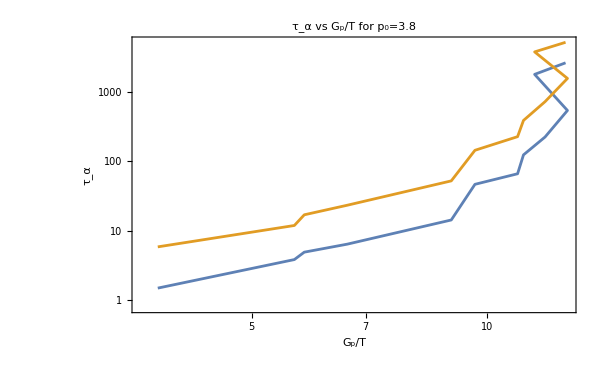
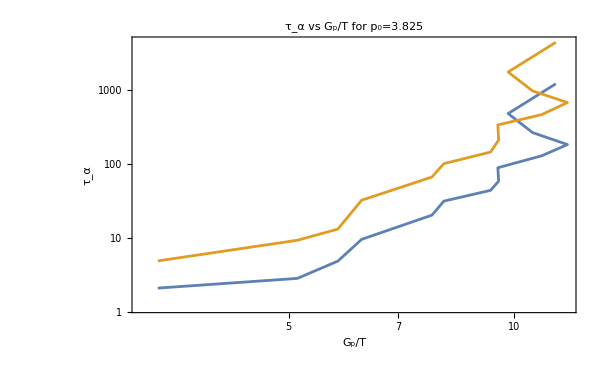
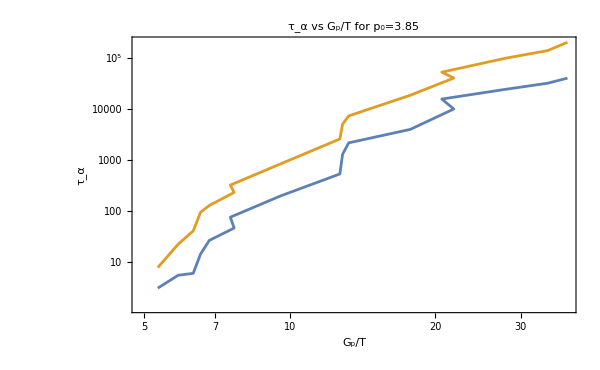

```mathematica
tauGpplots=Table[ListLogLogPlot[{Table[{fitting[[p,T]]["BestFitParameters"][[1,2]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{fitting[[p,T]]["BestFitParameters"][[1,2]]/temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"G_p/T","τ_α"},ImageSize->600,PlotLabel->"τ_α vs G_p/T for p_0="<>ToString[p0s[[p]]],ImageSize->600,Joined->True],{p,Length[p0s]}]
```

```mathematica
Gp=Table[Table[fitting[[p,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Gpfits=Table[{NonlinearModelFit[Table[{temperatures[[p,T]],Gp[[p,T]]},{T,1,4}],{A*x^B},{A,B},x],NonlinearModelFit[Table[{temperatures[[p,T]],Gp[[p,T]]},{T,5,10}],{A*x^B},{A,B},x]},{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…]}}

```mathematica
end={5,4,3};
```

```mathematica
taufitoverlap=Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]-end[[p]]}],{A Exp[B t^(1-Gpfits[[p,2]]["BestFitParameters"][[2,2]])]},{B,A},t],{p,Length[p0s]}]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
taufitSISF=Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T]]},{T,Length[temperatures[[p]]]-end[[p]]}],{A Exp[B t^(1-Gpfits[[p,2]]["BestFitParameters"][[2,2]])]},{B,A},t],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
taufit[[1]]
```

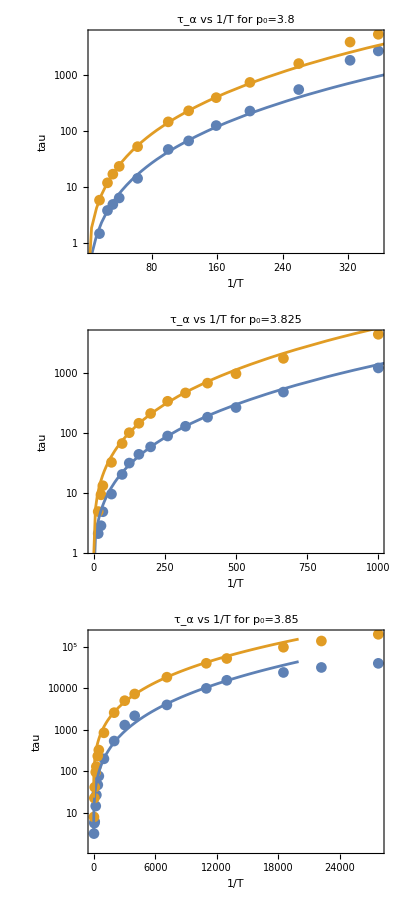

```mathematica
taufitPlots=Table[Show[ListLogPlot[{Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"1/T","tau "},ImageSize->600,PlotLabel->"τ_α vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->All(*PlotLegends->"Exp[T^-"<>ToString[NumberForm[1-Gpfits[[p,2]]["BestFitParameters"][[2,2]],2]]<>"]"*)],LogPlot[{taufitSISF[[p]][t],taufitoverlap[[p]][t]},{t,0.01,20000}]],{p,1,3}];
Column[taufitPlots]
```

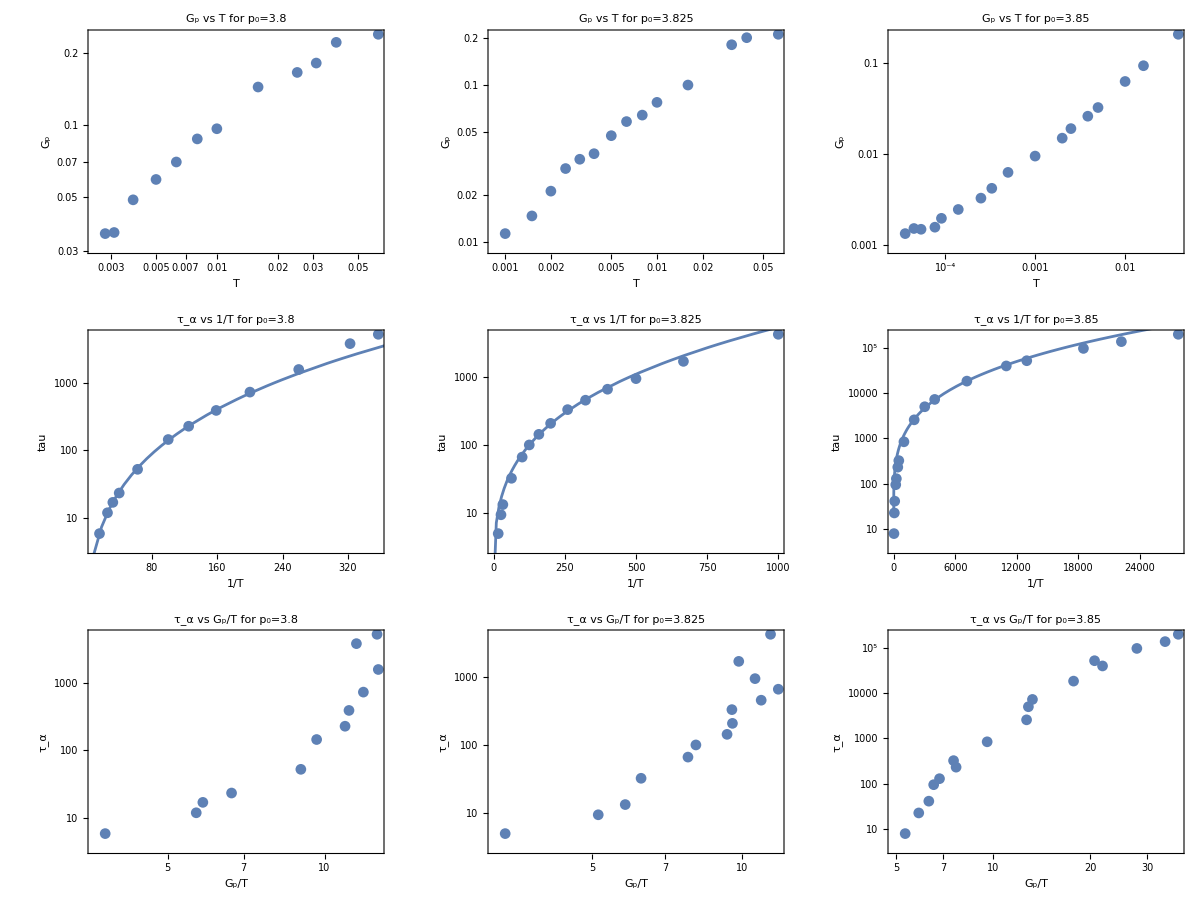

```mathematica
results=Grid[Partition[Flatten[{GPlots,taufitPlots,tauGpplots}],3]]
```

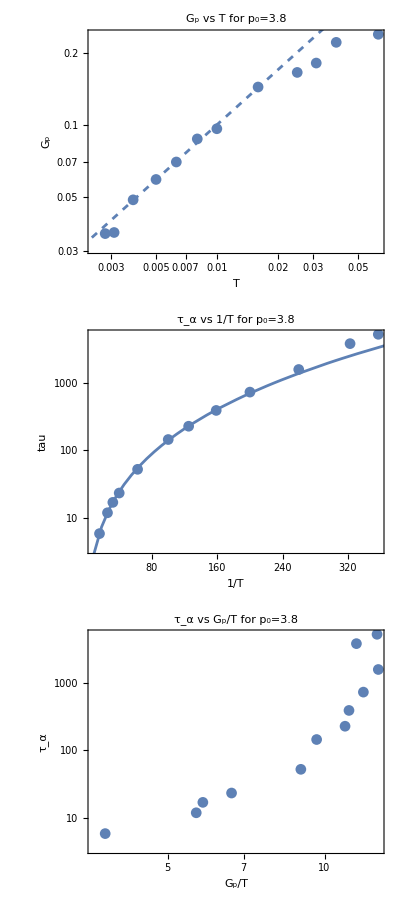

```mathematica
Column[{GPlots[[1]],taufitPlots[[1]],tauGpplots[[1]]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/05312024/Gpresults"<>ToString[p0s[[p]]]<>".jpeg",Column[{GPlots[[p]],taufitPlots[[p]],tauGpplots[[p]]}],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05312024/Gpresults3.8.jpeg,/home/chengling/Research/updates/05312024/Gpresults3.825.jpeg,/home/chengling/Research/updates/05312024/Gpresults3.85.jpeg}

```mathematica
Export["/home/chengling/Research/updates/05312024/TauPLots.jpeg",Column[Table[Show[ListLogLogPlot[{Table[{temperatures[[p,T]],tauAlphaCRSISF[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],tauG[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"1/T","tau "},ImageSize->600,PlotLegends->{"CRSISF","CRoverlap","tau_G"},PlotLabel->"τ_α vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->All(*PlotLegends->"Exp[T^-"<>ToString[NumberForm[1-Gpfits[[p,2]]["BestFitParameters"][[2,2]],2]]<>"]"*)]],{p,1,3}]],ImageResolution->800]
```

/home/chengling/Research/updates/05312024/TauPLots.jpeg